## Introduction

Analyze sync state

## Simulation

$Aborted

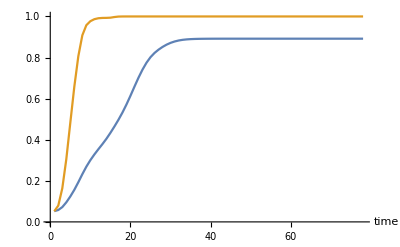

```mathematica
(*Preamble*)
{dt,n,T}={0.25,300,200}; 
{J,k}={3,3};
{e,b}={0,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / n,{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
results=plotResults[znew,pin]
]

ListPlot[{Abs[Wp],Abs[Wm]},Joined->True,AxesLabel->{"time"},LabelStyle->15]
```

```mathematica
{x,theta}=znew;
{ξ1,η1}={x+theta,x-theta};
α1=pin[[1]];
```

## Analysis

### Warm up: turn off b

```mathematica
Clear[vx,e,α,x,θ,b]
```

```mathematica
vx=e-b Sin[x-α]+sp j/2 Sin[ϕp-(x+θ)]+sm j/2 Sin[ϕm-(x-θ)];
vtheta=e-b Sin[θ-α]+sp k/2 Sin[ϕp-(x+θ)]-sm k/2 Sin[ϕm-(x-θ)];
es=Simplify[{vx, vtheta}/.e->0/.j->k/.ϕp->0/.ϕm->0];
TableForm[es]
```

1/2 (-2 b Sin[x-α]-sm Sin[x-θ]-sp Sin[x+θ])
1/2 (sm Sin[x-θ]+2 b Sin[α-θ]-sp Sin[x+θ])

```mathematica
Solve[(es/.b->0)==0,{x,θ}]//TableForm
```

x→ConditionalExpression[2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-π-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-π/2-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[π/2-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-π/2-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[π/2-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-π-2 π C[2], C[2]∈ℤ]

### Turn on b

#### Old coords

```mathematica
Clear[vx,e,α,x,θ,b,k,sp,sm,ϕp,ϕm];
vx=e-b Sin[x-α]+sp k/2 Sin[ϕp-(x+θ)]+sm k/2 Sin[ϕm-(x-θ)];
vtheta=e-b Sin[θ-α]+sp k/2 Sin[ϕp-(x+θ)]-sm k/2 Sin[ϕm-(x-θ)];
es=Simplify[{vx, vtheta}/.e->0/.j->k];
TableForm[es]
```

-b Sin[x-α]-1/2 k (sm Sin[x-θ-ϕm]+sp Sin[x+θ-ϕp])
1/2 (2 b Sin[α-θ]+k sm Sin[x-θ-ϕm]-k sp Sin[x+θ-ϕp])

```mathematica
xidot=Simplify[es[[1]]+es[[2]]/.b->1]
```

-Sin[x-α]+Sin[α-θ]-k sp Sin[x+θ-ϕp]

```mathematica
TrigFactor[-Sin[x-α]+Sin[α-θ]]
```

-2 Cos[x/2-θ/2] Sin[x/2-α+θ/2]

```mathematica
-2 Cos[x/2-θ/2] Sin[x/2-α+θ/2]
```

```mathematica
etadot=Simplify[es[[1]]-es[[2]]/.b->1]
```

-Sin[x-α]-Sin[α-θ]-k sm Sin[x-θ-ϕm]

```mathematica
TrigFactor[-Sin[x-α]-Sin[α-θ]]
```

-2 Cos[x/2-α+θ/2] Sin[x/2-θ/2]

#### In (ξ, η) coords

```mathematica
Clear[ξ,η,k,sp,sm,ϕp,ϕm,α];
esnew={
-2 Cos[η/2]Sin[ξ/2-α]+k sp Sin[ϕp-ξ],
-2 Sin[η/2]Cos[ξ/2-α]+k sm Sin[ϕm-η]
};
fp=Solve[(esnew/.ϕp->0/.ϕm->0/.α->0)==0,{ξ,η}]
```

{{ξ→ConditionalExpression[4 π C[2], C[2]∈ℤ],η→ConditionalExpression[4 π C[1], C[1]∈ℤ]},{ξ→ConditionalExpression[4 π C[2], C[2]∈ℤ],η→ConditionalExpression[2 (π+2 π C[1]), C[1]∈ℤ]},{ξ→ConditionalExpression[4 π C[2], C[2]∈ℤ],η→ConditionalExpression[2 (ArcTan[-1/(k sm),-(√(-1+k^2 sm^2))/(k sm)]+2 π C[1]), C[1]∈ℤ]},{ξ→ConditionalExpression[4 π C[2], C[2]∈ℤ],η→ConditionalExpression[2 (ArcTan[-1/(k sm),(√(-1+k^2 sm^2))/(k sm)]+2 π C[1]), C[1]∈ℤ]},{ξ→ConditionalExpression[2 (-π/2+2 π C[2]), C[2]∈ℤ],η→ConditionalExpression[2 (-π/2+2 π C[1]), C[1]∈ℤ]},{ξ→ConditionalExpression[2 (-π/2+2 π C[2]), C[2]∈ℤ],η→ConditionalExpression[2 (π/2+2 π C[1]), C[1]∈ℤ]},{ξ→ConditionalExpression[2 (π/2+2 π C[2]), C[2]∈ℤ],η→ConditionalExpression[2 (-π/2+2 π C[1]), C[1]∈ℤ]},{ξ→ConditionalExpression[2 (π/2+2 π C[2]), C[2]∈ℤ],η→ConditionalExpression[2 (π/2+2 π C[1]), C[1]∈ℤ]},{ξ→ConditionalExpression[2 (π+2 π C[2]), C[2]∈ℤ],η→ConditionalExpression[4 π C[1], C[1]∈ℤ]},{ξ→ConditionalExpression[2 (π+2 π C[2]), C[2]∈ℤ],η→ConditionalExpression[2 (π+2 π C[1]), C[1]∈ℤ]},{ξ→ConditionalExpression[2 (π+2 π C[2]), C[2]∈ℤ],η→ConditionalExpression[2 (ArcTan[1/(k sm),-(√(-1+k^2 sm^2))/(k sm)]+2 π C[1]), C[1]∈ℤ]},{ξ→ConditionalExpression[2 (π+2 π C[2]), C[2]∈ℤ],η→ConditionalExpression[2 (ArcTan[1/(k sm),(√(-1+k^2 sm^2))/(k sm)]+2 π C[1]), C[1]∈ℤ]},{ξ→ConditionalExpression[2 (ArcTan[-1/(k sp),-(√(-1+k^2 sp^2))/(k sp)]+2 π C[2]), C[2]∈ℤ],η→ConditionalExpression[4 π C[1], C[1]∈ℤ]},{ξ→ConditionalExpression[2 (ArcTan[-1/(k sp),(√(-1+k^2 sp^2))/(k sp)]+2 π C[2]), C[2]∈ℤ],η→ConditionalExpression[4 π C[1], C[1]∈ℤ]},{ξ→ConditionalExpression[2 (ArcTan[1/(k sp),-(√(-1+k^2 sp^2))/(k sp)]+2 π C[2]), C[2]∈ℤ],η→ConditionalExpression[2 (π+2 π C[1]), C[1]∈ℤ]},{ξ→ConditionalExpression[2 (ArcTan[1/(k sp),(√(-1+k^2 sp^2))/(k sp)]+2 π C[2]), C[2]∈ℤ],η→ConditionalExpression[2 (π+2 π C[1]), C[1]∈ℤ]}}

```mathematica
TrigExpand[Cos[α1-ξ]]
```

Cos[α1] Cos[ξ]+Sin[α1] Sin[ξ]

```mathematica
Manipulate[Plot[{2Sin[α1-y/2],k2 s2 Sin[y]},{y,-π,π},Epilog->{Line[{{α1,-2},{α1,2}}]}],{{s2,1},0,1},{k2,0.5,4},{{α1,π/4},-π,π}]
```

```mathematica
subs1={η->0,sm->1,ϕm->0,ϕp->0};
esnew/.subs1
```

{2 Sin[α-ξ/2]-k sp Sin[ξ],0}

```mathematica
Clear[α,k]
fp=Solve[2 Sin[α-ξ/2]-k sp Sin[ξ]==0,ξ];
Length[fp]
```

```mathematica
Cos[ξ/2]/.fp/.sp->0.8/.α->0.5/.k->2.5//Chop
```

{-0.877583,-0.877583,-0.636742,-0.636742,-0.349401,-0.349401,0.986143,0.986143}

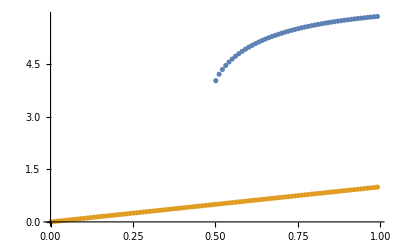

```mathematica
temp=(Cos[ξ/2]^2-Sin[ξ/2]^2)/.fp[[1]];
sub={k->4};
ss=Table[s,{s,0.001,1,0.01}];
rhs=Table[NIntegrate[(Cos[ξ/2]^2-Sin[ξ/2]^2)/.fp[[7]]/.sp->s/.sub,{α,0,2π}]//Quiet,{s,ss}];
ListPlot[{{ss,rhs}ᵀ,{ss,ss}ᵀ}]
```

```mathematica
e1=2(1-Cos[α-ξ])==k^2 sp^2(1-Cos[ξ]^2);
fp=Solve[e1,ξ];
Length[fp]
Cos[ξ]/.fp
```

```mathematica
fp[[1]]
```

{ξ→-2 ArcCos[-Cos[α]/(2 k sp)-1/2 √(Cos[α]^2/(k^2 sp^2)-(2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2))/(3 k^2 sp^2)+(2^(1/3) (-1+k^2 sp^2)^2)/(3 k^2 sp^2 (108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3+√(-4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^6+(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3)^2))^(1/3))+1/(3 2^(1/3) k^2 sp^2)(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3+√(-4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^6+(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3)^2))^(1/3))-1/2 √((2 Cos[α]^2)/(k^2 sp^2)-(4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2))/(3 k^2 sp^2)-(2^(1/3) (-1+k^2 sp^2)^2)/(3 k^2 sp^2 (108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3+√(-4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^6+(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3)^2))^(1/3))-1/(3 2^(1/3) k^2 sp^2)(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3+√(-4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^6+(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3)^2))^(1/3)-((16 Cos[α])/(k sp)-(8 Cos[α]^3)/(k^3 sp^3)+(8 Cos[α] (-k^2 sp^2+Cos[α]^2+Sin[α]^2))/(k^3 sp^3))/(4 √(Cos[α]^2/(k^2 sp^2)-(2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2))/(3 k^2 sp^2)+(2^(1/3) (-1+k^2 sp^2)^2)/(3 k^2 sp^2 (108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3+√(-4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^6+(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3)^2))^(1/3))+1/(3 2^(1/3) k^2 sp^2)(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3+√(-4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^6+(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3)^2))^(1/3))))]}

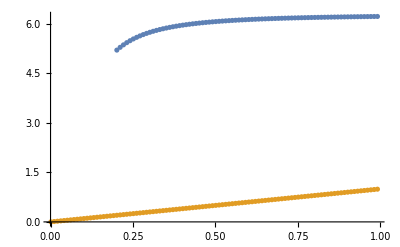

```mathematica
sub={k->10};
ss=Table[s,{s,0.001,1,0.01}];
rhs=Table[NIntegrate[Cos[ξ]/.fp[[8]]/.sp->s/.sub,{α,0,2π}]//Quiet,{s,ss}];
ListPlot[{{ss,rhs}ᵀ,{ss,ss}ᵀ}]
```

```mathematica
Clear[k];
(esnew/.ϕm->0/.ϕp->0/.η->0)//TableForm
fp=Solve[(esnew/.ϕp->0/.ϕm->0/.η->0)==0,{ξ,η}];
Length[fp]
```

2 Sin[α-ξ/2]-k sp Sin[ξ]
0

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
fp[[1]]
```

{ξ→-2 ArcCos[-Cos[α]/(2 k sp)-1/2 √(Cos[α]^2/(k^2 sp^2)-(2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2))/(3 k^2 sp^2)+(2^(1/3) (-1+k^2 sp^2)^2)/(3 k^2 sp^2 (108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3+√(-4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^6+(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3)^2))^(1/3))+1/(3 2^(1/3) k^2 sp^2)(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3+√(-4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^6+(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3)^2))^(1/3))-1/2 √((2 Cos[α]^2)/(k^2 sp^2)-(4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2))/(3 k^2 sp^2)-(2^(1/3) (-1+k^2 sp^2)^2)/(3 k^2 sp^2 (108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3+√(-4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^6+(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3)^2))^(1/3))-1/(3 2^(1/3) k^2 sp^2)(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3+√(-4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^6+(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3)^2))^(1/3)-((16 Cos[α])/(k sp)-(8 Cos[α]^3)/(k^3 sp^3)+(8 Cos[α] (-k^2 sp^2+Cos[α]^2+Sin[α]^2))/(k^3 sp^3))/(4 √(Cos[α]^2/(k^2 sp^2)-(2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2))/(3 k^2 sp^2)+(2^(1/3) (-1+k^2 sp^2)^2)/(3 k^2 sp^2 (108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3+√(-4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^6+(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3)^2))^(1/3))+1/(3 2^(1/3) k^2 sp^2)(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3+√(-4 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^6+(108 k^4 sp^4 Cos[α]^2-108 k^2 sp^2 Cos[α]^4+108 k^2 sp^2 Cos[α]^2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)+2 (-k^2 sp^2+Cos[α]^2+Sin[α]^2)^3)^2))^(1/3))))]}

```mathematica
cp=(Cos[ξ/2]^2-Sin[ξ/2]^2)/.fp[[1]];
Simplify[cp,Assumptions->{-π≤α≤π,k∈Reals}];
```

$Aborted

General::munfl: ArcCos[-0.504846+6.04006×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[-0.547358+1.06031×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[-0.588501+4.83566×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

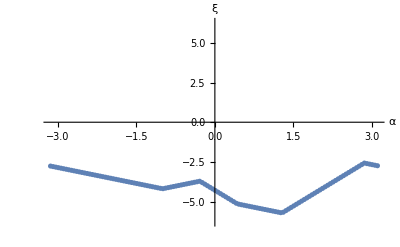

```mathematica
data=Table[{α,ξ/.fp[[3]]/.sp->0.8/.k->2.5/.ϕp->1},{α,-π,π,0.05}];
ListPlot[data,AxesLabel->{"α","ξ"},LabelStyle->15,PlotRange->{-2π,2π}]
```

```mathematica
Solve[y^4+a3 y^3+a1 y -1==0,y]
```

{{y→-a3/4-1/2 √(a3^2/4+(2^(1/3) (-4-a1 a3))/((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))+((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))/(3 2^(1/3)))-1/2 √(a3^2/2-(2^(1/3) (-4-a1 a3))/((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))-((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))/(3 2^(1/3))-(-8 a1-a3^3)/(4 √(a3^2/4+(2^(1/3) (-4-a1 a3))/((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))+((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))/(3 2^(1/3)))))},{y→-a3/4-1/2 √(a3^2/4+(2^(1/3) (-4-a1 a3))/((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))+((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))/(3 2^(1/3)))+1/2 √(a3^2/2-(2^(1/3) (-4-a1 a3))/((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))-((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))/(3 2^(1/3))-(-8 a1-a3^3)/(4 √(a3^2/4+(2^(1/3) (-4-a1 a3))/((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))+((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))/(3 2^(1/3)))))},{y→-a3/4+1/2 √(a3^2/4+(2^(1/3) (-4-a1 a3))/((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))+((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))/(3 2^(1/3)))-1/2 √(a3^2/2-(2^(1/3) (-4-a1 a3))/((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))-((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))/(3 2^(1/3))+(-8 a1-a3^3)/(4 √(a3^2/4+(2^(1/3) (-4-a1 a3))/((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))+((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))/(3 2^(1/3)))))},{y→-a3/4+1/2 √(a3^2/4+(2^(1/3) (-4-a1 a3))/((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))+((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))/(3 2^(1/3)))+1/2 √(a3^2/2-(2^(1/3) (-4-a1 a3))/((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))-((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))/(3 2^(1/3))+(-8 a1-a3^3)/(4 √(a3^2/4+(2^(1/3) (-4-a1 a3))/((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))+((27 a1^2-27 a3^2+√(-4 (-12-3 a1 a3)^3+(27 a1^2-27 a3^2)^2))^(1/3))/(3 2^(1/3)))))}}

## Self consistency equation

### Fixed points

```mathematica
Clear[α,k,ξ,sp];
fp=Solve[2Sin[α-ξ/2]+k sp Sin[ϕ-ξ]==0,ξ];
Length[fp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

8

Which one is physical?

General::munfl: ArcCos[-0.985117-1.84747×10^-19 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[-0.99359+5.72252×10^-19 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[-0.998556+9.68893×10^-19 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

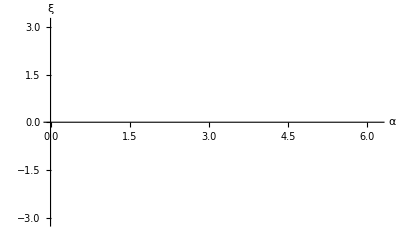
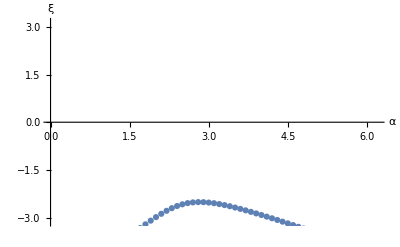
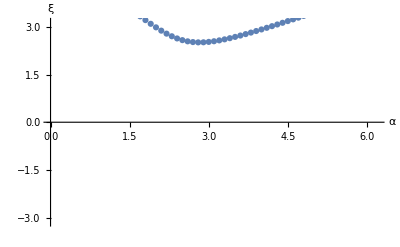
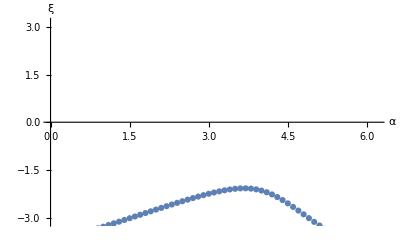
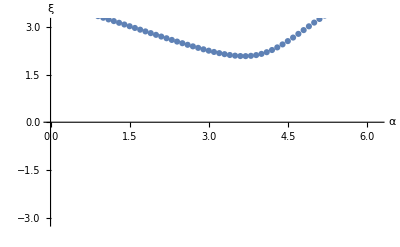
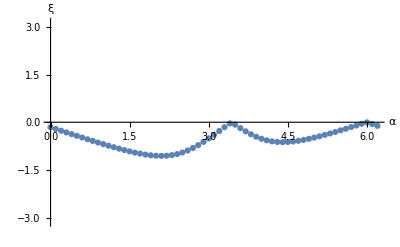
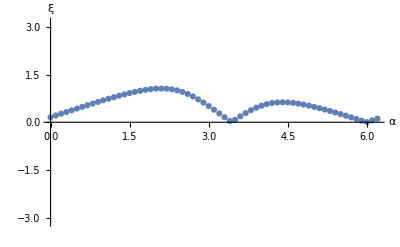
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
data=Table[{α,ξ}/.fp[[i]]/.{sp->Abs[Wp][[-1]],k->3,α->α1,ϕ->Arg[Wp][[-1]]},{α1,0,2π,0.1}];
ListPlot[data,AxesLabel->{"α","ξ"},LabelStyle->15,PlotRange->{-π,π}],
{i,1,Length[fp],1}
]
```

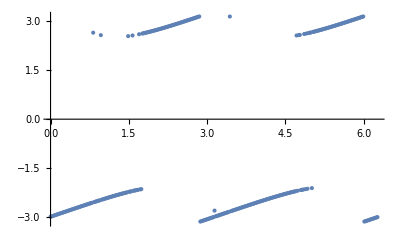

```mathematica
ListPlot[{α1,Mod[ξ1,2π]-π}ᵀ,PlotRange->{-π,π}]
```

### Integral equation

```mathematica
Clear[α,k,ξ,sp];
fp=Solve[2Sin[α-ξ/2]-k sp Sin[ξ]==0,ξ];
Length[fp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

8

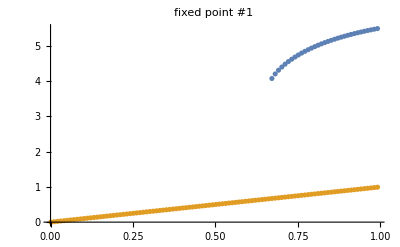
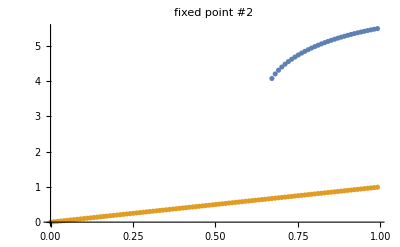
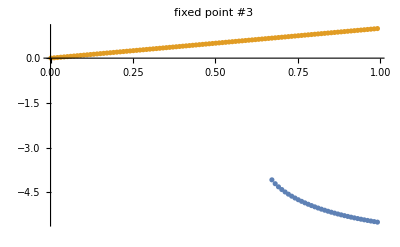
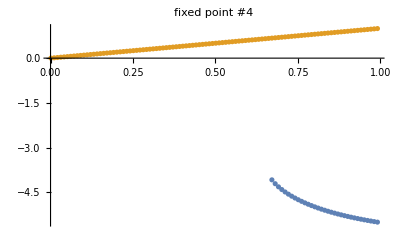
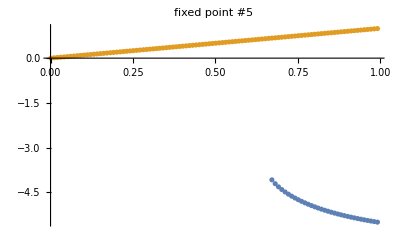
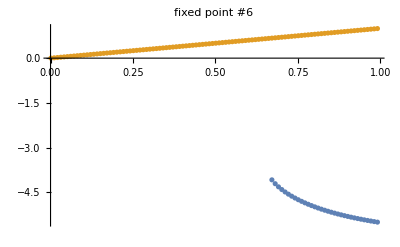
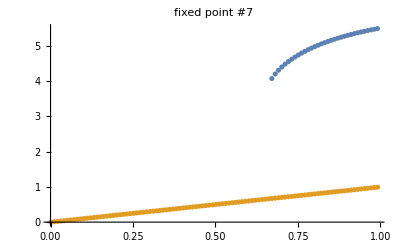
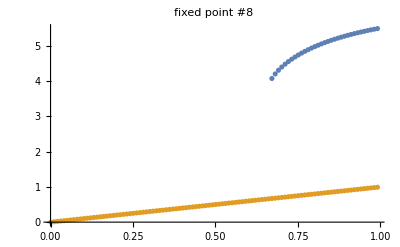

```mathematica
ParallelTable[
sub={k->3,ϕ->0};
ss=Table[s,{s,0.001,1,0.01}];
rhs=Table[NIntegrate[Cos[ξ]/.fp[[i]]/.sp->s/.sub,{α,0,2π}]//Quiet,{s,ss}];
ListPlot[{{ss,rhs}ᵀ,{ss,ss}ᵀ},PlotLabel->"fixed point #"<>ToString[i]],
{i,1,Length[fp]}
]
```

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex - b1*Sin[ z[[1,i]]-pin[[1,i]]];
vel[[2,i]] = Eθ - b2*Sin[ z[[2,i]]-pin[[2,i]] ];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[Mod[{x+θ,x-θ}ᵀ,2π],PlotRange->{{0,2π},{0,2π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];


findWaveSpeed[ϕ_,dt_]:=Block[{vel,index,data},
index=Round[0.25*Length[ϕ]];
data=ϕ[[index;;-1]];
vel=Differences[data]/dt;
Return[Median[vel]]
];

findVmean[xs_,thetas_]:=Module[{vx,vtheta,tcutoff,vxMean,vthetaMean,vMean},
{vx,vtheta}={{},{}};
tcutoff=Round[0.9Dimensions[xs][[2]]];
vxMean=Table[Mean[Differences[xs[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vthetaMean=Table[Mean[Differences[thetas[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vMean=√(vxMean^2+vthetaMean^2);
Return[vMean]
]
```